```mathematica
m = 9*^-31;
a = 0.001*^-15;
hbar = 1.05457*^-34;
(*v = 1*^12;*)
(*α = m v a / (2 π^2 hbar);*)
Ei = π^2  hbar^2 / (2 m a^2);
f[v_]:=∑_(n=1)^1000 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z])/E^(I m v a / (2 π^2 hbar) z^2),{z,0,Pi}]]^2;
```

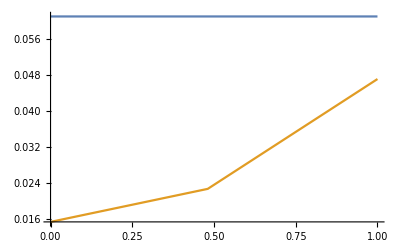

```mathematica
Plot[{Ei,f[v]} , {v,0,1*^15}, PlotPoints -> 3, MaxRecursion-> 0]
```

```mathematica
f[1*^15]
```

0.0470454

```mathematica
Speak["Done"]
```

Superposition quantification (superposition rank) below this line ----------------------------

Plotting the magnitude of the coefficients for the first 1000 levels for v = 0 (adiabatic)

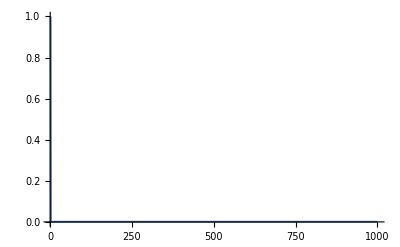

```mathematica
DiscretePlot[2/π  Abs[Integrate[(Sin[n z] Sin[z])/E^(I m 0 a / (2 π^2 hbar) z^2),{z,0,Pi}]], {n,1,1000}, PlotRange->Automatic]
```

Plotting the magnitude of the coefficients for the first 1000 levels for v = c (sudden)

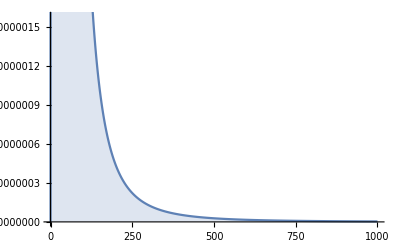

```mathematica
DiscretePlot[2/π  Abs[Integrate[(Sin[n z] Sin[z])/E^(I m 1*^15 a / (2 π^2 hbar) z^2),{z,0,Pi}]] , {n,0,1000},  PlotRange->Automatic]
```

New measure: 1 - |c0|: vary velocity and see what happens. For v = 0, we expect that the wavefuntion is the ground state of the new well, so 1-|c0| = 0 -- 0 superposition according to this measure.

```mathematica
1- 2/π  Abs[Integrate[(Sin[1 z] Sin[z])/E^(I m 1*^15 a / (2 π^2 hbar) z^2),{z,0,Pi}]]
```

```mathematica
DiscretePlot[1 - 2/π  Abs[Integrate[(Sin[z] Sin[z])/E^(I m v a / (2 π^2 hbar) z^2),{z,0,Pi}]] , {v,0,1*^15,0.001*^15},  PlotRange->Automatic]
```

```mathematica
Speak["Done with second computation"]
```

Testing stuff below this line -------------------------------

Energy of well with width 2a:

```mathematica
hbar^2 / (2 m a^2) π^2 / 4
```

0.0152447

Energy of well with width a:

```mathematica
hbar^2 / (2 m a^2) π^2
```

0.0609787

Testing the peculiarity with the Abs function (no Abs. sum from 1 to infinity)

```mathematica
∑_(n=1)^∞ n^2  (Integrate[(Sin[n z] Sin[z]),{z,0,Pi}])^2
```

π^2/4

Testing the peculiarity with the Abs function (no Abs. sum from 2 to infinity (for n=1 there a removable singularity anyway. IT’S NOT ZERO. YOU CAN’T JUST TAKE IT OUT). Actually it seems that only the n=1 term contributes to the sum)

```mathematica
∑_(n=1)^∞ n^2  (Integrate[(Sin[n z] Sin[z]),{z,0,Pi}])^2
```

π^2/4

Testing the peculiarity with the Abs function (Abs)

```mathematica
∑_(n=1)^∞ n^2  Abs[(Integrate[(Sin[n z] Sin[z]),{z,0,Pi}])]^2
```

Power::infy: Infinite expression 1/0 encountered.

∑_(n=1)^∞ n^2 Abs[Sin[n π]/(-1+n^2)]^2

Testing the peculiarity with the Abs function (Abs. Written differently. Credits to the stackexchange commenter)

```mathematica
Assuming[n>0,Sum[n^2 Abs[(Integrate[(Sin[n z] Sin[z]),{z,0,Pi}])]^2,{n,1,∞}]]
```

π^2/4

Testing the peculiarity with the Abs function (Abs. Written differently. Credits to the stackexchange commenter. Now adding in the exponential term. Exponential term does not give a close form.)

```mathematica
Assuming[n>0,Sum[n^2 Abs[(Integrate[(Sin[n z] Sin[z]) /E^(I α z^2) ,{z,0,Pi}])]^2,{n,1,∞}]]
```

∑_(n=1)^∞ 1/64 n^2 π Abs[ⅇ^(1/4 ⅈ (1+n)^2) Erfi[1/2 (-1)^(3/4) (1+n-2 π)]+ⅇ^(1/4 ⅈ (-1+n)^2) Erfi[1/2 (-1)^(3/4) (1-n+2 π)]+ⅇ^(1/4 ⅈ (-1+n)^2) Erfi[1/2 (-1)^(3/4) (-1+n+2 π)]-ⅇ^(1/4 ⅈ (1+n)^2) Erfi[1/2 (-1)^(3/4) (1+n+2 π)]]^2

Now we decide upto what n we should sum. We know that, for v = 0, we should get f[0] = ground energy of new well (0.0152447). It does not give the right answer.

```mathematica
f[v_]:=∑_(n=1)^100 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z])/E^(I α z^2),{z,0,Pi}]]^2;
f[0]
```

0.0499887

Now we decide upto what n we should sum. We know that, for v = 0, we should get f[0] = ground energy of new well (0.0152447).Trying with the exponential term manually removed. It gives the right answer.

```mathematica
f[v_]:=∑_(n=1)^10 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z]),{z,0,Pi}]]^2;
f[10]
```

0.0152447

Now we decide upto what n we should sum. We know that, for v = 0, we should get f[0] = ground energy of new well (0.0152447).Trying with α manually set to 0. It gives the right answer.

```mathematica
f[v_]:=∑_(n=1)^10 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z])/E^(I 0 z^2),{z,0,Pi}]]^2;
f[0]
```

0.0152447

Now we decide upto what n we should sum. We know that, for v = 0, we should get f[0] = ground energy of new well (0.0152447).Trying with α manually set to v. It gives the right answer.

```mathematica
f[v_]:=∑_(n=1)^10 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z])/E^(I v z^2),{z,0,Pi}]]^2;
f[0]
```

0.0152447

Now we decide upto what n we should sum. We know that, for v = 0, we should get f[0] = ground energy of new well (0.0152447).Trying with α manually set to what it represents. It gives the right answer! Ok we’re going to do it this way.

```mathematica
f[v_]:=∑_(n=1)^10 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z])/E^(I m v a / (2 π^2 hbar) z^2),{z,0,Pi}]]^2;
f[0]
```

0.0152447

Now we decide upto what n we should sum. We know that, for v = 0, we should get f[0] = ground energy of new well (0.0152447).Trying with α manually set to what it represents. This (summing up to 10) gives the right answer for v = 0. But it does not give the right answer for a large v, which makes sense because the faster the well expands, the more the wavefunction is going to be in superposition of all the levels of the new well.

```mathematica
f[v_]:=∑_(n=1)^10 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z])/E^(I m v a / (2 π^2 hbar) z^2),{z,0,Pi}]]^2;
f[0]
```

0.0152447

```mathematica
f[100000]
```

0.0152447

Now we decide upto what n we should sum. We know that, for v = 0, we should get f[0] = ground energy of new well (0.0152447).Trying with α manually set to what it represents. Summing upto 1000 gives an much better answer for a large v.

```mathematica
f[v_]:=∑_(n=1)^1000 hbar^2 / (2 m a^2)n^2  Abs[Integrate[(Sin[n z] Sin[z])/E^(I m v a / (2 π^2 hbar) z^2),{z,0,Pi}]]^2;
```

```mathematica
f[100000]
```

0.0590382